```mathematica
returnFunc[n_]:=Module[
{aRand,aSum,A,b},
aRand=RandomReal[1,{n,n}];
aSum= (aRand+Transpose[aRand])/2;
A=aSum+3 IdentityMatrix[n];
b=RandomReal[10,n];
f = Function[vec,1/2+Transpose[vec].A.vec-b.vec];
{f, A, b}
]

n=2;
plotN=100;
 
{f, A, b} =returnFunc[n];

If[
n<=1||n>=7,
Print[],
If[n==2,
Plot3D[f[{x,y}],{x,-plotN,plotN},{y,-plotN,plotN}],
If[n==3,
ContourPlot3D[f[{x,y,z}],{x,-plotN,plotN},{y,-plotN,plotN},{z,-plotN,plotN} ],
Print[]
]
]
];
```

```mathematica
heavyBall[func_,x0_,alpha_,beta_,maxIter_,tol_]:=Module[
{x,xPrev,xNew,trajectory,iter,grad,errors,h=10^-5,n=Length[x0]},numericGrad[x_]:=Table[(func[x+h*UnitVector[n,i]]-func[x-h*UnitVector[n,i]])/(2h),{i,n}];

xPrev=x0;
grad=numericGrad[x0];
x=x0-alpha*grad;
trajectory={xPrev,x};
errors={Norm[grad]};

For[iter=1,iter<=maxIter,iter++,
grad=numericGrad[x];
xNew=x-alpha*grad+beta*(x-xPrev);
AppendTo[errors,Norm[grad]];
AppendTo[trajectory,xNew];

If[Norm[xNew-x]<tol,
Print["Достигнута точность! Iter: ", iter];
Break[]
];
xPrev=x;
x=xNew;
];
{x,trajectory,errors}
];

nesterov[func_,x0_,alpha_,beta_,maxIter_,tol_]:=Module[
{x,xPrev,y,trajectory,iter,grad,errors,h=10^-5,n=Length[x0]},
numericGrad[x_]:=Table[(func[x+h*UnitVector[n,i]]-func[x-h*UnitVector[n,i]])/(2 h),{i,n}];

xPrev=x0;
x=x0;
trajectory={x0};
errors={};

For[iter=1,iter<=maxIter,iter++,
y=x+beta*(x-xPrev);
grad=numericGrad[y];
xNew=y-alpha*grad;
AppendTo[errors,Norm[grad]];
AppendTo[trajectory,xNew];

If[Norm[xNew-x]<tol,Print["Достигнута точность! Iter: ",iter];
Break[]
];
xPrev=x;
x=xNew;
];
{x,trajectory,errors}
]


conjugateGradient[func_,x0_,maxIter_,tol_]:=Module[
{x,grad,gradPrev,d,alpha, beta,trajectory,errors,iter,h=10^-5,n=Length[x0]},numericGrad[x_]:=Table[(func[x+h*UnitVector[n,i]]-func[x-h*UnitVector[n,i]])/(2 h),{i,n}];
x=x0;
grad=numericGrad[x];
d=-grad;
trajectory={x0};
errors={Norm[grad]};
For[iter=1,iter<=maxIter,iter++,
alpha=0.1;
x=x+alpha*d;
gradPrev=grad;
grad=numericGrad[x];
beta=(grad.grad)/(gradPrev.gradPrev);
d=-grad+beta*d;
AppendTo[trajectory,x];
AppendTo[errors,Norm[grad]];
If[Norm[grad]<tol,
Print["Достигнута точность! Iter: ",iter];
Break[]];];
{x,trajectory,errors}
]

x0={500, 1000};
alpha=0.1;
beta=0.8;
maxIter=1000;
tol=10^-5;
```

Достигнута точность! Iter: 146

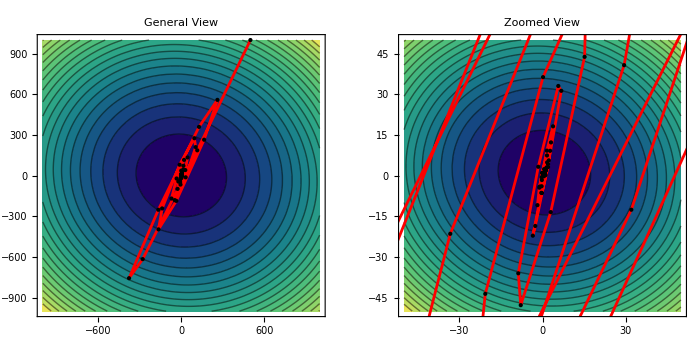

```mathematica
resultBall=heavyBall[f,x0,alpha,beta,maxIter,tol];

xMin = resultBall[[1]];
trajectory=resultBall[[2]];

plot=ListPlot[
trajectory,
PlotStyle->Directive[Red,PointSize[Small]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];


generalPlot=ContourPlot[f[{x,y}],{x,-1000,1000},{y,-1000,1000},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"General View"];
zoomedPlot=ContourPlot[f[{x,y}],{x,-50,50},{y,-50,50},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"Zoomed View"];

show = Show[GraphicsRow[{Show[generalPlot,plot],Show[zoomedPlot,plot]}],ImageSize-> 700]


animation=ListAnimate[
Table[
Show[
ContourPlot[
f[{x,y}],{x,-300,300},{y,-300,300}, Contours->20
],
Graphics[
{Black,PointSize[Large],
Point[trajectory[[i]]],Red,Line[trajectory[[1;;i]]],
Text["Шаг: "<>ToString[i],Scaled[{0.1,0.9}]
]
}
]
],
{i,0,Length[trajectory],5}
]
];

(*Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/2dAnimationBall.gif",animation,"GIF","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];
Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/trackBall",show,"PNG","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];*)
```

Достигнута точность! Iter: 23

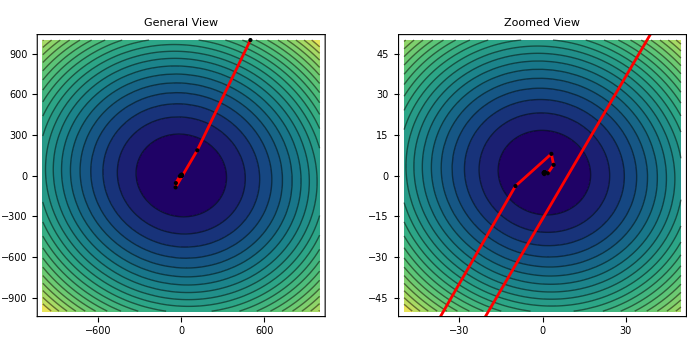

```mathematica
resultNesterov =  nesterov[f,x0,alpha,beta,maxIter,tol];

xMin = resultNesterov[[1]];
trajectory=resultNesterov[[2]];

plot=ListPlot[
trajectory,
PlotStyle->Directive[Red,PointSize[Small]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];

generalPlot=ContourPlot[f[{x,y}],{x,-1000,1000},{y,-1000,1000},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"General View"];

zoomedPlot=ContourPlot[f[{x,y}],{x,-50,50},{y,-50,50},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"Zoomed View"];

show = Show[GraphicsRow[{Show[generalPlot,plot],Show[zoomedPlot,plot]}],ImageSize-> 700]

animation=ListAnimate[
Table[
Show[
ContourPlot[
f[{x,y}],{x,-50,50},{y,-50,50}, Contours->20
],
Graphics[
{Black,PointSize[Large],
Point[trajectory[[i]]],Red,Line[trajectory[[1;;i]]],
Text["Шаг: "<>ToString[i],Scaled[{0.1,0.9}]
]
}
]
],
{i,0,Length[trajectory],1}
]
];

(*Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/2dАnimationNesterov.gif",animation,"GIF","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];
Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/trackNesterov.png",show,"PNG","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];*)
```

Достигнута точность! Iter: 12

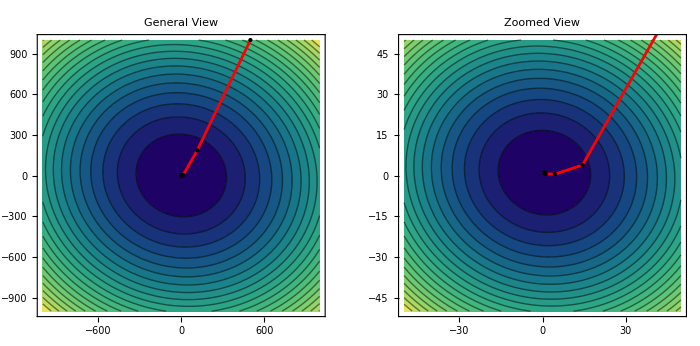

```mathematica
resultGrad =conjugateGradient[f,x0, maxIter,tol];

xMin = resultGrad[[1]];
trajectory=resultGrad[[2]];

plot=ListPlot[
trajectory,
PlotStyle->Directive[Red,PointSize[Small]],
PlotRange->All,
AxesLabel->{"x1","x2"},
Joined->True,
Mesh->All,
MeshStyle->Directive[Black,Thickness[0.00001]]
];


generalPlot=ContourPlot[f[{x,y}],{x,-1000,1000},{y,-1000,1000},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"General View"];

zoomedPlot=ContourPlot[f[{x,y}],{x,-50,50},{y,-50,50},Contours->20,ColorFunction->"BlueGreenYellow",PlotLabel->"Zoomed View"];

show = Show[GraphicsRow[{Show[generalPlot,plot],Show[zoomedPlot,plot]}],ImageSize-> 700]

animation=ListAnimate[
Table[
Show[
ContourPlot[
f[{x,y}],{x,-300,300},{y,-300,300}, Contours->20
],
Graphics[
{Black,PointSize[Large],
Point[trajectory[[i]]],Red,Line[trajectory[[1;;i]]],
Text["Шаг: "<>ToString[i],Scaled[{0.1,0.9}]
]
}
]
],
{i,0,Length[trajectory],1}
]
];

Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/2dАnimationGradients.gif",animation,"GIF","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];
Export["/home/eva/Documents/ITMO/2_course/MetodsOptimus/lab3/images/trackGradients.png",show,"PNG","DisplayDurations"->0.1,"AnimationRepetitions"->Infinity];*)
```

```mathematica
|
```